## myPackage

```mathematica
(*generated 2025-06-13, by Dr.Carl Firle, MD*)
filename="data_preparation";
CloudGet[CloudObject["https://www.wolframcloud.com/obj/firlecarl/myPackageWL.wl"]]

myFontSize=13
myFontStandard="Lucida Sans Unicode"

myStyle["Wolfram Mathematica Version 14.2",22,Background->Yellow]
(*myColorFavorits=TableForm[Table[ColorData[i],{i,{3,24,35,61,97,106,114}}]] Table[ContourPlot[x+Sin[x^2+y^2],{x,-4,4},{y,-4,4},Contours->9,ContourShading->ColorData[i,"ColorList"]],{i,{3,24,35,61,97,106,114}}] myColorGradientFavorits=Table[DensityPlot[y+Sin[x^2+3y],{x,-3,3},{y,-3,3},ColorFunction->ColorData[i]],{i,{"RedBlueTones","Rainbow","DarkRainbow","DarkBands","BrightBands","CMYKColors","Pastel","GrayTones"}}] Table[ColorData[i,"Image"],{i,{"DarkRainbow","Pastel"}}]*)

myColors=ColorData[61]
myColorForGradient=ColorData["DarkRainbow"]
myCMYKColors[]
myBAUAColors[4]
myPureColors[]

myExportFigureList={};
myExportEquationList={};

impPath=Directory[]~~"\\Desktop\\source\\" (*path of source*)
exPath=Directory[]~~"\\Desktop\\output\\" (*path of output*)

pathSaveVersions=Directory[]~~"\\Desktop\\backup\\" (*path of backup*)
NotebookOpen[CloudObject["https://www.wolframcloud.com/obj/firlecarl/myBackup.nb"]]

NotebookSave[EvaluationNotebook[],Directory[]~~"\\Desktop\\"~~filename~~".nb"]

myPackageInputPrint[]
```

13

Lucida Sans Unicode

Wolfram Mathematica Version 14.2

ColorDataFunction[…]

ColorDataFunction[…]

{CMYKColor[{0, 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0.09, 1, 0.03],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]}

{RGBColor[0.10196078431372549, 0.4392156862745098, 0.7215686274509804],RGBColor[0.38823529411764707, 0.38823529411764707, 0.3843137254901961],RGBColor[0.9568627450980393, 0.9529411764705882, 0.9254901960784314],RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.4588235294117647, 0.7450980392156863, 0.9176470588235294],RGBColor[0.9254901960784314, 0.4, 0.09019607843137255],RGBColor[0.9450980392156862, 0.7019607843137254, 0.],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.06666666666666667, 0.3058823529411765, 0.5058823529411764],RGBColor[0.00392156862745098, 0.3607843137254902, 0.5764705882352941],RGBColor[0.6509803921568628, 0.8196078431372549, 0.9450980392156862],RGBColor[0.8117647058823529, 0.8980392156862745, 0.9725490196078431]}

{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 0.5, 0],RGBColor[0, 1, 1],RGBColor[1, 0, 1],RGBColor[1, 1, 0],GrayLevel[0]}

C:\Users\mona_\Desktop\source\

C:\Users\mona_\Desktop\output\

C:\Users\mona_\Desktop\backup\

myAroundString[l_List/;Dimensions[l]⟦2⟧==2]:=Module[{},(StringJoin[ToString[#1⟦1⟧]~~ ± ~~ToString[#1⟦-1⟧]]&)/@l]
myBAUAColors[a_Integer:5]:=Module[{bauaMainColors,bauaHighlightColors,bauaBlueColors,bauaAllColors,bauaDesignColors,bauaCMYKColors},{bauaMainColors→{RGBColor[#1A70B8],RGBColor[#636362],RGBColor[#F4F3EC],RGBColor[#E3E5DB],RGBColor[#ABD18F]},bauaHighlightColors→{RGBColor[#EC6617],RGBColor[#75BEEA],RGBColor[#ABD18F],RGBColor[#F1B300]},bauaBlueColors→{{RGBColor[#114e81],RGBColor[#015c93],RGBColor[#1770b8],RGBColor[#74bdea],RGBColor[#a6d1f1],RGBColor[#cfe5f8]}},bauaAllColors→{RGBColor[#1A70B8],RGBColor[#636362],RGBColor[#F4F3EC],RGBColor[#E3E5DB],RGBColor[#ABD18F],RGBColor[#75BEEA],RGBColor[#EC6617],RGBColor[#F1B300],RGBColor[#ABD18F],RGBColor[#114e81],RGBColor[#015c93],RGBColor[#a6d1f1],RGBColor[#cfe5f8]},bauaDesignColors→{RGBColor[0.4588235294117647, 0.7450980392156863, 0.9176470588235294],RGBColor[0.9254901960784314, 0.4, 0.09019607843137255],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.9450980392156862, 0.7019607843137254, 0.],RGBColor[0.10196078431372549, 0.4392156862745098, 0.7215686274509804],RGBColor[0.38823529411764707, 0.38823529411764707, 0.3843137254901961],RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],RGBColor[0.8117647058823529, 0.8980392156862745, 0.9725490196078431],RGBColor[0.06666666666666667, 0.3058823529411765, 0.5058823529411764]},bauaCMYKColors→{CMYKColor[0.85, 0.5, 0, 0],CMYKColor[0.85, 0.5, 0, 0, 0.7],CMYKColor[0.85, 0.5, 0, 0, 0.4],CMYKColor[0.85, 0.45, 0, 0.3],CMYKColor[0.85, 0.5, 0, 0.4],CMYKColor[0.85, 0.45, 0, 0.3, 0.7],CMYKColor[0.85, 0.45, 0, 0.3, 0.5],CMYKColor[0.85, 0.45, 0, 0.3, 0.3],CMYKColor[0., 0., 0, 0.75],CMYKColor[0., 0., 0.05, 0.06],CMYKColor[0.08, 0.03, 0.12, 0.07],CMYKColor[0.62, 0.27, 0.92, 0.7],CMYKColor[0.55, 0.1, 0, 0],CMYKColor[0., 0.75, 1, 0],CMYKColor[0., 0.3, 1, 0.05],CMYKColor[0.4, 0., 0.55, 0]}}⟦a,2⟧]
myCMYKColors[a_Integer:1]:=Module[{},{{CMYKColor[{0, 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0.09, 1, 0.03],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]},{Leuchtgelb→CMYKColor[{0, 0, 1, 0}],Zitronengelb→CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],Orange→CMYKColor[{0, Rational[11, 20], 1, 0}],Hellrosa→CMYKColor[{Rational[1, 20], Rational[2, 5], Rational[1, 5], 0}],Altrosa→CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],Feuerrot→CMYKColor[{0, 1, 1, Rational[1, 5]}],Signalrot→CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],Korallenrot→CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],Leuchtrot→CMYKColor[{0, Rational[9, 10], 1, 0}],Reines Rot→CMYKColor[{0, 1, Rational[9, 10], 0}],Weinrot→CMYKColor[{Rational[7, 20], 1, Rational[13, 20], 0}],Pink→CMYKColor[{0, 1, 0, 0}],Lila→CMYKColor[{Rational[1, 2], Rational[3, 5], 0, 0}],Violett→CMYKColor[{Rational[3, 5], Rational[9, 10], 0, Rational[1, 10]}],Azurblau→CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],Himmelblau→CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],Reines Blau→CMYKColor[{1, Rational[7, 10], 0, 0}],Nachtblau→CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],Pastelltürkis→CMYKColor[{Rational[3, 5], Rational[1, 10], Rational[1, 2], 0}],Minttürkis→CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],Türkis→CMYKColor[{Rational[9, 10], Rational[1, 10], Rational[2, 5], Rational[1, 10]}],Leuchtgrün/Gelbgrün→CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],Grün→CMYKColor[{Rational[9, 10], 0, Rational[4, 5], 0}],Grasgrün→CMYKColor[{Rational[9, 10], Rational[1, 5], 1, Rational[1, 4]}],Maigrün→CMYKColor[{Rational[4, 5], Rational[1, 5], 1, Rational[1, 10]}],Rotbraun→CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],Kastanienbraun→CMYKColor[{0, Rational[3, 5], Rational[3, 5], Rational[7, 10]}],Schokobraun→CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],Cremeweiß→CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],Beige→CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],Silbergrau→CMYKColor[{Rational[1, 10], 0, 0, Rational[2, 5]}],Steingrau→CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],Tiefschwarz→CMYKColor[{Rational[2, 5], Rational[1, 5], Rational[1, 5], 1}]},{Leuchtgelb→{CMYKColor[{0, 0, 1, 0}]},Zitronengelb→{CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}]},Orange→{CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{0, Rational[1, 2], 1, 0}],CMYKColor[{0, Rational[11, 20], 1, 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{0, Rational[13, 20], 1, 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}]},Hellrosa→{CMYKColor[{Rational[1, 20], Rational[2, 5], Rational[1, 5], 0}],CMYKColor[{0, Rational[1, 2], Rational[1, 5], Rational[1, 10]}]},Altrosa→{CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[7, 10], Rational[3, 10], Rational[1, 10]}],CMYKColor[{0, Rational[13, 20], Rational[2, 5], Rational[1, 10]}]},Feuerrot→{CMYKColor[{0, 1, 1, Rational[1, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}]},Signalrot→{CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[1, 5], 1, Rational[9, 10], Rational[1, 10]}]},Korallenrot→{CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[3, 10]}]},Leuchtrot→{CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[{0, 1, 1, 0}]},Reines Rot→{CMYKColor[{0, 1, Rational[9, 10], 0}],CMYKColor[{0, 1, Rational[7, 10], 0}]},Weinrot→{CMYKColor[{Rational[1, 5], 1, Rational[4, 5], Rational[2, 5]}],CMYKColor[{Rational[2, 5], 1, Rational[3, 5], Rational[2, 5]}],CMYKColor[{Rational[7, 20], 1, Rational[13, 20], 0}],CMYKColor[{Rational[3, 5], 1, Rational[4, 5], 0}]},Pink→{CMYKColor[{0, 1, 0, 0}]},Lila→{CMYKColor[{Rational[1, 2], Rational[3, 5], 0, 0}],CMYKColor[{Rational[3, 5], Rational[7, 10], Rational[1, 20], Rational[1, 10]}]},Violett→{CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, Rational[1, 10]}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[9, 10], 1, 0, 0}]},Azurblau→{CMYKColor[{Rational[9, 10], Rational[3, 10], Rational[1, 10], Rational[2, 5]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, Rational[3, 10]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}]},Himmelblau→{CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[9, 10], Rational[1, 2], 0, 0}],CMYKColor[{1, Rational[3, 10], 0, Rational[1, 10]}],CMYKColor[{1, Rational[2, 5], 0, 0}]},Reines Blau→{CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{1, Rational[7, 10], 0, 0}],CMYKColor[{1, Rational[4, 5], 0, 0}],CMYKColor[{Rational[19, 20], Rational[3, 5], 0, Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, Rational[2, 5]}]},Nachtblau→{CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{1, 1, Rational[2, 5], Rational[2, 5]}]},Pastelltürkis→{CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[3, 5], Rational[1, 10], Rational[1, 2], 0}],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], Rational[1, 5]}]},Minttürkis→{CMYKColor[{Rational[4, 5], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{Rational[7, 10], Rational[3, 20], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}]},Türkis→{CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[7, 20], Rational[1, 5]}],CMYKColor[{Rational[9, 10], Rational[1, 10], Rational[2, 5], Rational[1, 10]}]},Leuchtgrün/Gelbgrün→{CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{Rational[3, 5], 0, Rational[19, 20], 0}],CMYKColor[{Rational[7, 10], 0, Rational[9, 10], 0}]},Grün→{CMYKColor[{Rational[13, 20], 0, Rational[4, 5], 0}],CMYKColor[{Rational[9, 10], 0, Rational[4, 5], 0}],CMYKColor[{Rational[17, 20], 0, 1, 0}],CMYKColor[{Rational[17, 20], 0, 1, Rational[1, 10]}]},Grasgrün→{CMYKColor[{Rational[3, 5], 0, Rational[9, 10], Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[21, 25], 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], 1, Rational[1, 4]}],CMYKColor[{Rational[7, 10], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}]},Maigrün→{CMYKColor[{Rational[4, 5], Rational[1, 5], 1, Rational[1, 10]}]},Rotbraun→{CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[1, 20], 1, 1, Rational[4, 5]}]},Kastanienbraun→{CMYKColor[{0, Rational[3, 5], Rational[3, 5], Rational[7, 10]}],CMYKColor[{Rational[1, 2], 1, 1, Rational[1, 2]}],CMYKColor[{0, Rational[9, 10], 1, Rational[4, 5]}]},Schokobraun→{CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{0, Rational[3, 5], Rational[9, 10], Rational[4, 5]}],CMYKColor[{Rational[2, 5], Rational[7, 10], Rational[3, 5], Rational[4, 5]}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{Rational[3, 5], Rational[4, 5], Rational[4, 5], Rational[4, 5]}]},Cremeweiß→{CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}]},Beige→{CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}]},Silbergrau→{CMYKColor[{Rational[1, 10], 0, 0, Rational[2, 5]}]},Steingrau→{CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}]},Tiefschwarz→{CMYKColor[{1, Rational[2, 5], Rational[2, 5], Rational[9, 10]}],CMYKColor[{Rational[2, 5], Rational[1, 5], Rational[1, 5], 1}],CMYKColor[{Rational[3, 10], 0, 0, 1}],CMYKColor[{0, Rational[1, 2], Rational[1, 5], 1}]}}}⟦a⟧]


myExportEquations[l_List]:=Module[{id,eq},((id=#1⟦2⟧;eq=#1⟦1⟧;Export[exPath~~\equations\~~id~~.txt,ExportString[eq,{MathML,Expression}]];If[MemberQ[myExportEquationList⟦All,1⟧,id],myExportEquationList=ReplacePart[myExportEquationList,FirstPosition[myExportEquationList⟦All,1⟧,id]⟦1⟧→{id,eq}];,AppendTo[myExportEquationList,{id,eq}]];)&)/@l Export[exPath~~\equations\##1 equation IDs and equations.pdf,Column[(Row[Riffle[{#1⟦1⟧,#1⟦2⟧},	]]&)/@myExportEquationList]];Export[exPath~~\equations\##2 equation IDs.rtf,StringRiffle[Prepend[myExportEquationList⟦All,1⟧,exPath~~\equations\],
]];]
myExportF[l_List]:=Module[{r,g,nameID,name,icon},((g=#1⟦1⟧;nameID=#1⟦2⟧;name=#1⟦3⟧;If[#1⟦5⟧==True,r=600;Table[Export[exPath~~CMYK ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi CMYK~~i,ColorConvert[Rasterize[g,ImageResolution→r],CMYK]],{i,{.eps,.png}}],Nothing];r=72;icon=Rasterize[g,ImageResolution→r];Table[Export[exPath~~ToString[i]~~ ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi~~i,icon],{i,{.png}}];r=150;Table[Export[exPath~~ToString[i]~~ ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}];r=#1⟦4⟧;Table[Export[exPath~~ToString[i]~~ ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}];(Table[Export[exPath~~ToString[i]~~\~~nameID~~i,g],{i,{.svg,.eps,.pdf}}]&)/@#1;If[MemberQ[myExportFigureList⟦All,1⟧,nameID],myExportFigureList=ReplacePart[myExportFigureList,FirstPosition[myExportFigureList⟦All,1⟧,nameID]⟦1⟧→{nameID,name,icon}];,AppendTo[myExportFigureList,{nameID,name,icon}]];)&)/@l;Export[exPath~~##1 full names of figure IDs.pdf,Column[Join[{		ID figure name,		_________},(Row[Riffle[{#1⟦1⟧,#1⟦2⟧,#1⟦3⟧},	]]&)/@myExportFigureList]]];Export[exPath~~##2 figure IDs.rtf,StringRiffle[myExportFigureList⟦All,1⟧,
]];]
myExportFPNG[l_List]:=Module[{r,g,name},((g=#1⟦1⟧;name=#1⟦2⟧;r=#1⟦3⟧;Table[Export[exPath~~name~~ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}])&)/@l]
myExportFSVG[l_List]:=Module[{r,g,name},((g=#1⟦1⟧;name=#1⟦2⟧;(Table[Export[exPath~~name~~i,g],{i,{.svg}}]&)/@#1)&)/@l]
myFlatten[l_List,level_Integer]:=Module[{},Map[Flatten[#1]&,l,{level}]]
myFrameStyle[fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},FrameStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myFrameTickStyle[fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},FrameTicksStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myLabelStyle[fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},LabelStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myLegendAppearance[markersize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},LegendAppearance→{LegendMarkerSize→markersize,FontFamily→fontfamily,color}]
myPackageInputPrint[]:=Module[{l},l=ToExpression/@(Select[Names[Global`*],StringContainsQ[my~~__]]/.{myExportFunctionList→Nothing,myExportFigureList→Nothing,myExportEquationList→Nothing,myFontSize→Nothing,myFontStandard→Nothing,myColors→Nothing,myFigureIDs→Nothing,myColorForGradient→Nothing,myPlotColors→Nothing});TableForm[Definition/@l]]

myPlotSequence[]:=Sequence[ImageSize→Large,Frame→True,myFrameStyle[],myFrameTickStyle[]]
myPlotStyle[opacity_:1,colorList_List:myPlotColors]:=Module[{},PlotStyle→(Directive[Opacity[opacity],#1]&)/@colorList]
myPureColors[]:={Red,Blue,Green,Orange,Cyan,Magenta,Yellow,Black}
myReplaceList[lTarget_List,fReplace_]:=Module[{},(#1→fReplace&)/@lTarget]
myStringJoin[l_List,deli_String:,start_Integer:2,end_Integer:-2,step_Integer:2]:=Module[{},StringJoin[Riffle[ToString/@l,deli,{start,end,step}]]]
myStringSplit[s_String,deli_List]:=Module[{i,out,j},i=1;out=StringSplit[s,deli⟦i⟧,All];For[j=1,j<Length[deli],j++,i++;out=Map[StringSplit[#1,deli⟦i⟧,All]&,out,{i-1}]];out]
myStringSplit202507[s_String,deli_List]:=Module[{i,out,j},i=1;out=StringSplit[s,deli⟦i⟧];For[j=1,j<Length[deli],j++,i++;out=Map[StringSplit[#1,deli⟦i⟧]&,out,{i-1}]];out]
myStyle[s_,fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},Style[If[StringQ[s],s,ToString[s]],FontSize→fontsize,FontFamily→fontfamily,color]]
mySubJoin[lTarget_List,lInsert_List,pos_Integer:1]:=Module[{},(Insert[lTarget⟦#1⟦2⟧⟧,#1⟦1⟧,pos]&)/@lInsert]
myT[l1_List,l2_List]:=Module[{},Transpose[{l1,l2}]]
myTake[lData_List,lSort_List]:=Module[{outList,dimensionQ},If[Length[Dimensions[lData]]>1,dimensionQ=True,dimensionQ=False];outList=If[dimensionQ===True,(If[Head[#1]===Span,lData⟦All,#1⟧,{lData⟦All,#1⟧}]&)/@lSort,(If[Head[#1]===Span,lData⟦#1⟧,{lData⟦#1⟧}]&)/@lSort];outList=(If[Length[#1]>1,Transpose[#1],#1]&)/@outList;outList=Transpose[Flatten[outList,1]]]
myTickStyle[fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},TicksStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myTranspose[lLong_List,lShort_List]:=Module[{},Transpose[{lLong,Table[lShort,Length[lLong]]}]]

## myFigureIDs

```mathematica
IntegerString[#,10,3]&/@Range[50]  (*make the next output cell to an input cell with the variable myFigureIDs myFigureIDs=*)
```

```mathematica
myFigureIDs={"001","002","003","004","005","006","007","008","009","010","011","012","013","014","015","016","017","018","019","020","021","022","023","024","025","026","027","028","029","030","031","032","033","034","035","036","037","038","039","040","041","042","043","044","045","046","047","048","049","050"};
```

## data import

```mathematica
synchronize=.
synchronize[l_List,timePosition_Integer,maxTime_,timeStamp_]:=Module[{l2}
,l2=l
;l2[[All,timePosition]]=Map[Round[timeStamp-Quantity[(maxTime-#),"Seconds"],.5]&,l2[[All,timePosition]]];
l2]

protocolSelect=.
protocolSelect[varName_String]:=Select[protocol,StringContainsQ[Keys[#],varName]&]

oneTableAppend=.
oneTableAppend[varNamesList_List,lValues_List]:=Module[{}
,varNames=Flatten[Append[varNames,varNamesList]]
;oneTable=myFlatten[Append[oneTable[[FirstPosition[timeline,#[[1]]][[1]]]],#[[2;;-1]]]&/@lValues,1];]

urlHead="https://raw.githubusercontent.com/Carl-Firle/effects-of-mask-wearing-on-human-particle-formation/refs/heads/main/raw-data/";
```

```mathematica
dProtocol=Import[urlHead ~~"2025-06-06/first-test-air-cleaner/%23testdata_protocol.txt"];
```

```mathematica
protocol=#[[1]]->Quantity[ToExpression[#[[2]]],"Seconds"]&/@myStringSplit[dProtocol,{" --- "," :: "}];
protocol=#[[1]]->#[[2]]-Min[Values@protocol]&/@protocol
```

```mathematica
dGrimm=Import[urlHead ~~"2025-06-06/first-test-air-cleaner/11-D_2025-06-06-C.dat","Text"];
dGrimm=myStringSplit[StringReplace[dGrimm,","->"."],{"\n","\t"}];
dGrimm[[16;;-1]]=Flatten[{UnixTime[FromDateString[#[[1]]]],ToExpression[#[[2;;-1]]]}]&/@dGrimm[[16;;-1]];
```

```mathematica
dSensirion=Import[urlHead ~~"test_data/2025-06-19_15-42-56-CC_AllSensors.edf","Text"];
dSensirionSave=dSensirion;
```

```mathematica
dSensirion=dSensirionSave
```

```mathematica
dSensirion=dSensirionSave;
dSensirion=myStringSplit[dSensirion,{"\n","\t"}];
dSensirion[[11;;-1]]=Flatten[{ToExpression[#[[1]]],FromDateString[#[[2]]],ToExpression[#[[3;;-1]]]}]&/@dSensirion[[11;;-1]];
dSensirionVarNames=Delete[dSensirion[[10]],2];
```

```mathematica
dSensirionSync=synchronize[dSensirion[[11;;-1]],1,Max[dSensirion[[11;;-1]][[All,1]]],UnitConvert["AS_02_end"/. protocol,"Seconds"]];
```

```mathematica
(*the timeline in test protocol is too wide*)
dSensirionSync=synchronize[dSensirion[[11;;-1]],1,Max[dSensirion[[11;;-1]][[All,1]]],Quantity[200,"Seconds"]];
```

```mathematica
dSensirionSync=myFlatten[Transpose[{Delete[Union/@(Transpose/@GatherBy[dSensirionSync,First][[All,All,1]]),-1],Delete[(Transpose/@GatherBy[dSensirionSync,First][[All,All,3;;-1]]) /. Null->Nothing,-1]}],1];
```

```mathematica
varNames[[1;;13]]
```

{elapsed time,MassConc_1p0_AS1_2740FCF491C5882D,MassConc_2p5_AS1_2740FCF491C5882D,MassConc_4p0_AS1_2740FCF491C5882D,MassConc_10p_AS1_2740FCF491C5882D,NumbConc_0p5_AS1_2740FCF491C5882D,NumbConc_1p0_AS1_2740FCF491C5882D,NumbConc_2p5_AS1_2740FCF491C5882D,NumbConc_4p0_AS1_2740FCF491C5882D,NumbConc_10p_AS1_2740FCF491C5882D,TypPartSize_AS1_2740FCF491C5882D,MassConc_1p0_AS2_1A7F561F1DADAE76,MassConc_2p5_AS2_1A7F561F1DADAE76}

```mathematica
(*data sheet https://sensirion.com/media/documents/8600FF88/64A3B8D6/Sensirion_PM_Sensors_Datasheet_SPS30.pdf and statementhttps://sensirion.com/media/documents/8600FF88/64A3B8D6/Sensirion_PM_Sensors_Datasheet_SPS30.pdfNonehttps://sensirion.com/media/documents/8600FF88/64A3B8D6/Sensirion_PM_Sensors_Datasheet_SPS30.pdfHyperlinkActionRecycledHyperlinkActive and precision
 https://sensirion.com/resource/application_note/pm/sensor_specificationhttps://sensirion.com/resource/application_note/pm/sensor_specificationNonehttps://sensirion.com/resource/application_note/pm/sensor_specificationHyperlinkActionRecycledHyperlinkActive*)

errorNumConcSensirionLowPM=.
errorNumConcSensirionLowPM[n_Real]:=Which[n<=1000,Around[n,100],1000<n<=3000,Around[n,n 0.25]]

{#[[1]],#[[2]]-#[[1]],#[[3]]-#[[2]],#[[4]]-#[[3]]}&/@dSensirionSync[[All,2;;5]]
{errorNumConcSensirionLowPM[#[[1]]],#[[2]]-#[[1]],#[[3]]-#[[2]],#[[4]]-#[[3]],#[[5]]-#[[4]]}&/@dSensirionSync[[All,6;;11]]
```

{{2.23504,0.370527,0.19496,0.100907},{2.22557,0.357792,0.185143,0.095826},{2.22397,0.3343,0.166299,0.086072},{2.21109,0.328975,0.162606,0.08416},{2.18524,0.321458,0.157749,0.081647},{2.17094,0.301574,0.142398,0.073702},{2.14676,0.309093,0.149573,0.077417},{2.11321,0.307111,0.149529,0.077393},{2.07277,0.295132,0.141754,0.073369},{2.05177,0.288751,0.137586,0.071212},{2.0196,0.289021,0.139292,0.072095},{1.99433,0.280837,0.133872,0.06929},{1.97071,0.291973,0.143933,0.074497},{1.9637,0.26669,0.123895,0.064125},{1.95268,0.279689,0.134875,0.069807},{1.94445,0.286584,0.140807,0.07288},{1.96135,0.271774,0.128099,0.066302}}

{{15.100.,2.709,0.313555,0.048063,0.010603},{15.100.,2.68075,0.300329,0.045878,0.010198},{15.100.,2.64393,0.275352,0.041714,0.009457},{15.100.,2.62354,0.270146,0.04087,0.009291},{15.100.,2.58735,0.263077,0.039737,0.009068},{15.100.,2.54372,0.242407,0.036319,0.008442},{14.100.,2.53173,0.251303,0.037848,0.008693},{14.100.,2.49643,0.250406,0.037764,0.00865},{14.100.,2.4395,0.239115,0.035953,0.00829},{14.100.,2.40969,0.233076,0.034988,0.008097},{13.100.,2.37912,0.234536,0.035291,0.008124},{13.100.,2.34249,0.226735,0.034037,0.007876},{13.100.,2.33646,0.239461,0.036205,0.008243},{13.100.,2.29175,0.21277,0.031768,0.007442},{13.100.,2.30065,0.227024,0.034166,0.007862},{13.100.,2.30308,0.234672,0.035456,0.008085},{13.100.,2.29712,0.218274,0.032691,0.007605}}

```mathematica
dSensirionSync[[1;;4]]
```

{{183. s,2.23504,2.60557,2.80053,2.90144,14.7791,17.4881,17.8017,17.8498,17.8604,0.576007,2.61877,2.76925,2.76925,2.76925,18.0863,20.835,20.9,20.9059,20.9093,0.416321,1.8758,2.24368,2.45312,2.56153,12.2488,14.6083,14.932,14.9825,14.9932,0.64579,2.55947,3.38518,3.93168,4.21454,15.835,19.5398,20.3263,20.4526,20.4775,0.618498,3.58191,4.17596,4.48859,4.65041,23.685,28.0265,28.5292,28.6063,28.6232,0.531587,2.66073,2.95696,3.07239,3.13214,17.9873,20.9947,21.2136,21.2451,21.2531,0.567381,2.58288,2.83898,2.92569,2.97057,17.5467,20.4187,20.5976,20.6226,20.6293,0.463908,2.36809,2.76949,2.98315,3.09375,15.6349,18.5186,18.8601,18.9126,18.924,0.640243},{184. s,2.22557,2.58336,2.7685,2.86433,14.7468,17.4275,17.7279,17.7737,17.7839,0.569088,2.60881,2.75871,2.75871,2.75871,18.0175,20.7557,20.8205,20.8263,20.8297,0.421999,1.8478,2.23111,2.45428,2.56979,12.0091,14.3648,14.706,14.7594,14.7706,0.655172,2.55613,3.31991,3.8167,4.07383,15.9796,19.5881,20.3088,20.4241,20.4471,0.605126,3.51104,4.06669,4.35167,4.49918,23.2888,27.5044,27.9687,28.0395,28.0553,0.52852,2.69664,2.98772,3.09735,3.15409,18.2549,21.2892,21.5013,21.5316,21.5394,0.563184,2.65672,2.92502,3.01815,3.06635,18.0351,20.9965,21.1857,21.2123,21.2193,0.463446,2.40917,2.80532,3.01286,3.12028,15.9393,18.8547,19.1891,19.2403,19.2516,0.636087},{185. s,2.22397,2.55827,2.72457,2.81064,14.7993,17.4432,17.7186,17.7603,17.7697,0.560369,2.59568,2.74483,2.74483,2.74483,17.9269,20.6513,20.7157,20.7215,20.7249,0.420604,1.85219,2.20399,2.40159,2.50386,12.1257,14.4382,14.7457,14.7935,14.8037,0.641935,2.58685,3.25396,3.67148,3.88758,16.4589,19.952,20.5685,20.6664,20.6863,0.57041,3.4486,3.96811,4.2269,4.36084,22.9458,27.047,27.4751,27.54,27.5547,0.523624,2.73987,3.01824,3.11562,3.16603,18.5948,21.6515,21.8486,21.8763,21.8836,0.553396,2.72149,3.00469,3.10681,3.15967,18.4521,21.4983,21.701,21.7296,21.7372,0.463827,2.45015,2.84176,3.04374,3.14829,16.241,19.1891,19.5171,19.5672,19.5784,0.632687},{186. s,2.21109,2.54007,2.70267,2.78683,14.7228,17.3464,17.6165,17.6574,17.6667,0.556985,2.60818,2.75805,2.75805,2.75805,18.0132,20.7507,20.8155,20.8213,20.8247,0.434151,1.8521,2.21166,2.41551,2.52102,12.1039,14.4281,14.7438,14.793,14.8035,0.644857,2.59317,3.23342,3.62901,3.83376,16.5765,20.0353,20.623,20.7161,20.7351,0.573515,3.368,3.87542,4.1282,4.25903,22.4094,26.4148,26.833,26.8964,26.9107,0.528187,2.76606,3.04883,3.14856,3.20017,18.7678,21.8564,22.0571,22.0854,22.0929,0.553242,2.8245,3.10121,3.19334,3.24102,19.1973,22.3329,22.525,22.5517,22.5589,0.457813,2.52533,2.89279,3.07184,3.16452,16.8375,19.8218,20.1213,20.1666,20.1769,0.611449}}

```mathematica
timeline=Range[0,(Values[protocolSelect["end of protocol"]]-Values[protocolSelect["start time"]]) [[1]][[1]],.5]//Short
varNames={"elapsed time"};
(*the time points in protocol were altered manually to ensure whole time line for test data*)
oneTable=List/@timeline
```

```mathematica
timeline=Quantity[#,"Seconds"]&/@Range[0,300,.5];
varNames={"elapsed time"};
oneTable=List/@timeline;
```

```mathematica
oneTableAppend[Rest@dSensirionVarNames,dSensirionSync]
```

```mathematica
varNames
```

{elapsed time,MassConc_1p0_AS1_2740FCF491C5882D,MassConc_2p5_AS1_2740FCF491C5882D,MassConc_4p0_AS1_2740FCF491C5882D,MassConc_10p_AS1_2740FCF491C5882D,NumbConc_0p5_AS1_2740FCF491C5882D,NumbConc_1p0_AS1_2740FCF491C5882D,NumbConc_2p5_AS1_2740FCF491C5882D,NumbConc_4p0_AS1_2740FCF491C5882D,NumbConc_10p_AS1_2740FCF491C5882D,TypPartSize_AS1_2740FCF491C5882D,MassConc_1p0_AS2_1A7F561F1DADAE76,MassConc_2p5_AS2_1A7F561F1DADAE76,MassConc_4p0_AS2_1A7F561F1DADAE76,MassConc_10p_AS2_1A7F561F1DADAE76,NumbConc_0p5_AS2_1A7F561F1DADAE76,NumbConc_1p0_AS2_1A7F561F1DADAE76,NumbConc_2p5_AS2_1A7F561F1DADAE76,NumbConc_4p0_AS2_1A7F561F1DADAE76,NumbConc_10p_AS2_1A7F561F1DADAE76,TypPartSize_AS2_1A7F561F1DADAE76,MassConc_1p0_AS4_82D8A7196C9B9F0B,MassConc_2p5_AS4_82D8A7196C9B9F0B,MassConc_4p0_AS4_82D8A7196C9B9F0B,MassConc_10p_AS4_82D8A7196C9B9F0B,NumbConc_0p5_AS4_82D8A7196C9B9F0B,NumbConc_1p0_AS4_82D8A7196C9B9F0B,NumbConc_2p5_AS4_82D8A7196C9B9F0B,NumbConc_4p0_AS4_82D8A7196C9B9F0B,NumbConc_10p_AS4_82D8A7196C9B9F0B,TypPartSize_AS4_82D8A7196C9B9F0B,MassConc_1p0_AS3_216C32DC0F46B10B,MassConc_2p5_AS3_216C32DC0F46B10B,MassConc_4p0_AS3_216C32DC0F46B10B,MassConc_10p_AS3_216C32DC0F46B10B,NumbConc_0p5_AS3_216C32DC0F46B10B,NumbConc_1p0_AS3_216C32DC0F46B10B,NumbConc_2p5_AS3_216C32DC0F46B10B,NumbConc_4p0_AS3_216C32DC0F46B10B,NumbConc_10p_AS3_216C32DC0F46B10B,TypPartSize_AS3_216C32DC0F46B10B,MassConc_1p0_SPS3x_2FEAD396CB2188C0,MassConc_2p5_SPS3x_2FEAD396CB2188C0,MassConc_4p0_SPS3x_2FEAD396CB2188C0,MassConc_10p_SPS3x_2FEAD396CB2188C0,NumbConc_0p5_SPS3x_2FEAD396CB2188C0,NumbConc_1p0_SPS3x_2FEAD396CB2188C0,NumbConc_2p5_SPS3x_2FEAD396CB2188C0,NumbConc_4p0_SPS3x_2FEAD396CB2188C0,NumbConc_10p_SPS3x_2FEAD396CB2188C0,TypPartSize_SPS3x_2FEAD396CB2188C0,MassConc_1p0_SPS3x_648B35C6F1901F98,MassConc_2p5_SPS3x_648B35C6F1901F98,MassConc_4p0_SPS3x_648B35C6F1901F98,MassConc_10p_SPS3x_648B35C6F1901F98,NumbConc_0p5_SPS3x_648B35C6F1901F98,NumbConc_1p0_SPS3x_648B35C6F1901F98,NumbConc_2p5_SPS3x_648B35C6F1901F98,NumbConc_4p0_SPS3x_648B35C6F1901F98,NumbConc_10p_SPS3x_648B35C6F1901F98,TypPartSize_SPS3x_648B35C6F1901F98,MassConc_1p0_SPS3x_5BD37108BAA89560,MassConc_2p5_SPS3x_5BD37108BAA89560,MassConc_4p0_SPS3x_5BD37108BAA89560,MassConc_10p_SPS3x_5BD37108BAA89560,NumbConc_0p5_SPS3x_5BD37108BAA89560,NumbConc_1p0_SPS3x_5BD37108BAA89560,NumbConc_2p5_SPS3x_5BD37108BAA89560,NumbConc_4p0_SPS3x_5BD37108BAA89560,NumbConc_10p_SPS3x_5BD37108BAA89560,TypPartSize_SPS3x_5BD37108BAA89560,MassConc_1p0_SPS3x_F865F7E1A40D8DB2,MassConc_2p5_SPS3x_F865F7E1A40D8DB2,MassConc_4p0_SPS3x_F865F7E1A40D8DB2,MassConc_10p_SPS3x_F865F7E1A40D8DB2,NumbConc_0p5_SPS3x_F865F7E1A40D8DB2,NumbConc_1p0_SPS3x_F865F7E1A40D8DB2,NumbConc_2p5_SPS3x_F865F7E1A40D8DB2,NumbConc_4p0_SPS3x_F865F7E1A40D8DB2,NumbConc_10p_SPS3x_F865F7E1A40D8DB2,TypPartSize_SPS3x_F865F7E1A40D8DB2}

```mathematica
Max[tab[[All,"time"]]]
```

1276.5 s

```mathematica
tab[All,"time"][[-5;;-2]]//InputForm
%/. (Head->List)
```

TabularColumn[…]

TabularColumn[<|"Data" -> {4, {{{1252.5, 1258.5, 1264.5, 1270.5}, {}, None}}, None}, 
  "ElementType" -> TypeSpecifier["Quantity"]["Real64", "Seconds"]|>]

```mathematica
tab[[All,"time"]] [[-1]]
```

1276.5 s

```mathematica
tab=ToTabular[d[[16;;-1]],"Rows",<|"ColumnKeys"->d[[15]] /. "[d&t31.12.2035 11:50:55]" -> "time"|>];
tab=CastColumns[%,#->"Quantity"::["Real64","Micrometers"]&/@(sizeRange=d[[15,2;;-1]])];
tab=TransformColumns[tab,{"time"->Function[Round[#time-Max[tab[[All,"time"]]]+UnitConvert["AS_01_end"/. protocol,"Seconds"],.5]]}]
```

```mathematica
Table[Missing[],Length@sizeRange]
```

{Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[]}

```mathematica
temp=tab[[207;;-1]]
```

```mathematica
Dimensions@temp
```

{7,32}

```mathematica
TabularRow[Table[Missing[],Dimensions[temp][[2]]]]
```

TabularRow[…]

```mathematica
Insert[temp,TabularRow[Table[Missing[],Dimensions[temp][[2]]]],3]
```

Insert::ins: Cannot insert at position {3} in Tabular[<7,32>]

Insert[,TabularRow[…],3]

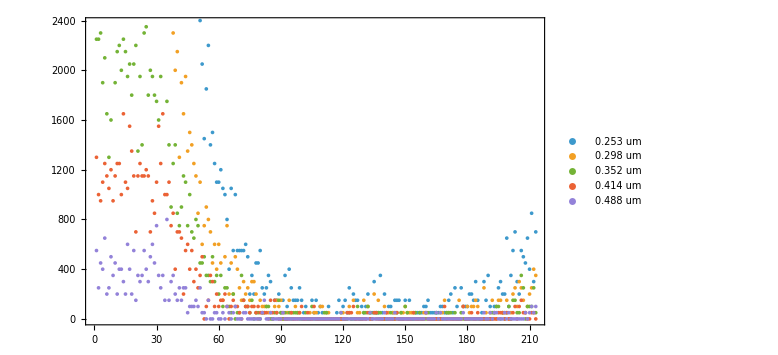

```mathematica
ListPlot[Transpose[Values/@(ConstructColumns[tab,sizeRange[[1;;5]]]//Normal)],myPlotSequence[],PlotLegends->sizeRange[[1;;5]]]
```